In order to create an autonomous function, we need to study all the maximum on f(t) as half maximum, this means considering them as interior points or maximum at the exterior. One needs to use the Corollary that arises from the study of the endpoints as f’(t)=0, we calculate the second derivate.

```mathematica
Clear[F1,F2,u,f5]
```

```mathematica
u[x_,t_]:=Exp[x*Cos[t]]
```

```mathematica
(Sqrt[1000]*N[Integrate[Exp[1000*Cos[t]],{t,Pi,3Pi}]])/(Exp[1000]*Sqrt[2*Pi])
```

1.00012507038585

```mathematica
Sqrt[x]*N[AsymptoticIntegrate[Exp[x*Cos[t]],{t,0,3*Pi},{x,0,10}]]/Exp[x]*Sqrt[2*Pi]
```

ⅇ^-x √(2 π) √x (9.42478+2.35619 x^2+0.147262 x^4+0.00409062 x^6+0.0000639159 x^8+6.39159×10^-7 x^10)

```mathematica
f5[x_]:=Integrate[u[x,t],{t,0,2*Pi}]/(Exp[x]*Sqrt[2])
```

```mathematica
AsymptoticIntegrate[u[x,t],{t,0,Pi},{x,0,10}]
```

π+(π x^2)/4+(π x^4)/64+(π x^6)/2304+(π x^8)/147456+(π x^10)/14745600

```mathematica
N[AsymptoticIntegrate[u[x,t],{t,0,Pi},{x,0,19}]/.x-> Pi]
```

17.2092

```mathematica
Integrate[u[2*Pi,t],{t,0,2*Pi}]/Pi
```

2 BesselI[0,2 π]

```mathematica
5.4778449719429485-F3[Pi]
```

5.47784-F3[π]

```mathematica
F1[x_]:=Ceiling[x/(2*Pi)]
```

```mathematica
F2[x_]:=Floor[x/(2*Pi)]
```

```mathematica
Table[F1[x]+F2[x],{x,0,8*Pi,Pi/2}]
```

{0,1,1,1,2,3,3,3,4,5,5,5,6,7,7,7,8}

```mathematica
F3[x_]:=(F1[x]+F2[x])*Exp[x]*Sqrt[Pi/(2*x)]
```

```mathematica
F3[1]
```

ⅇ √(π/2)

```mathematica
N[ⅇ^π √(π/2)]
```

29.0026

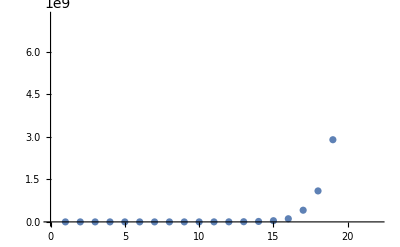

```mathematica
ListPlot[Table[F3[x],{x,Pi,8Pi}]]
```

```mathematica
N[Integrate[Exp[1000*Cos[t]],{t,Pi,8*Pi}]]
```

5.46630922499356×10^433

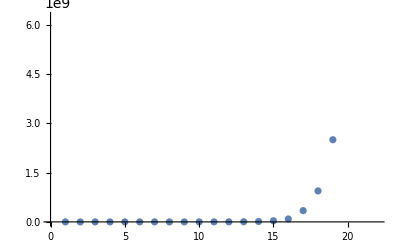

```mathematica
ListPlot[Table[Integrate[Exp[x*Cos[t]],{t,Pi,x}],{x,Pi,8*Pi}]]
```

```mathematica
AsymptoticEquivalent[F3[x],Integrate [Exp[x*Cos[t]],{t,Pi,x}],x-> Infinity]
```

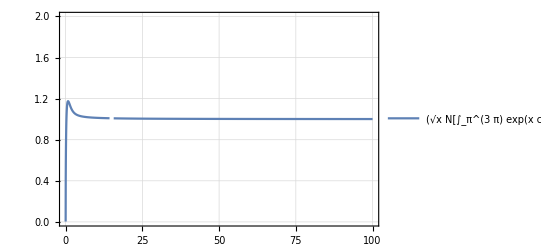

```mathematica
Plot[(Sqrt[x]*N[Integrate[Exp[x*Cos[t]],{t,Pi,3Pi}]])/(Exp[x]*Sqrt[2*Pi]),{x,0,100},PlotTheme->"Detailed",PlotRange->{0,2}]
```